```mathematica
Manipulate[With[{Q0=20 10^7,c=2.99792458×10^8,λ=680×10^-9,ϵ=6 10^-6,κ=1.1,P=10^-3,n=1.45,α=0.00018,ρ=2200,Cp=966,Vc=300 10^-18,S=100 10^-12},With[{ωc=(2π×c)/λ},With[{κ0=ωc/Q0},With[{κ1=x κ0},sol=NDSolve[{a'[t]==ⅈ (100κ0-500κ0(1-8/π^2 Sum[Cos[i π v t/1000/κ0]/i^2,{i,1,20,2}])+ωc ϵ T[t]) a[t]-(κ0+κ1)/2 a[t]-√κ1 ,T'[t]==-κ/(Cp ρ S) T[t]+(P α c)/(Cp ρ Vc n) Abs[ a[t]]^2,a[0]==0,T[0]==0},{a,T},{t,0,2000 κ0/v}];Plot[{Abs[1+√κ1 a[t]/.sol]^2,0.5(1-8/π^2 Sum[Cos[i π v t/1000/κ0]/i^2,{i,1,20,2}]),v t/1000/κ0},{t,0,2000 κ0/v},PlotRange->{0,2}]]]]],{{x,1},0,10},{{v,2π 50 10^11},10^11,10^14}]
```

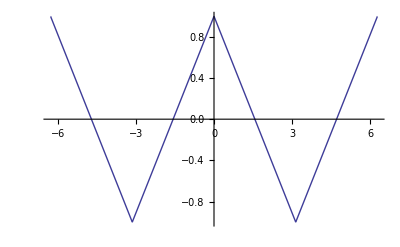

```mathematica
Plot[8/π^2 Sum[Cos[i x]/i^2,{i,1,200,2}],{x,-2π,2π}]
```

```mathematica
Manipulate[With[{Q0=20 10^7,c=2.99792458×10^8,λ=680×10^-9,ϵ=6 10^-6,κ=1.1,P=10^-3,n=1.45,α=0.00018,ρ=2200,Cp=966,Vc=300 10^-18,S=100 10^-12},With[{ωc=(2π×c)/λ},With[{κ0=ωc/Q0},With[{κ1=x κ0},sol=NDSolve[{a'[t]==ⅈ (50κ0-v t+ωc ϵ T[t]) a[t]-(κ0+κ1)/2 a[t]-√κ1 ,T'[t]==-κ/(Cp ρ S) T[t]+(P α c)/(Cp ρ Vc n) Abs[ a[t]]^2,a[0]==0,T[0]==0},{a,T},{t,0,2000 κ0/v}];Plot[{Abs[1+√κ1 a[t]/.sol]^2,0.5(1-8/π^2 Sum[Cos[i π v t/1000/κ0]/i^2,{i,1,20,2}]),v t/1000/κ0},{t,0,2000 κ0/v},PlotRange->{0,2}]]]]],{{x,1},0,10},{{v,2π 50 10^11},10^11,10^14}]
```